```mathematica
psi[x_,a_,A_]:=Piecewise[{{A x/a,0<x<a/2},{A (1-x/a),a/2<x<a}}]
```

```mathematica
psi[x,a,A]
```

Piecewise[{{(A x)/a, 0<x<a/2}, {A (1-x/a), a/2<x<a}, {0, True}}]

```mathematica
ψ(x)=Piecewise[{{(A x)/a, 0<x<a/2}, {A (1-x/a), a/2<x<a}}]
```

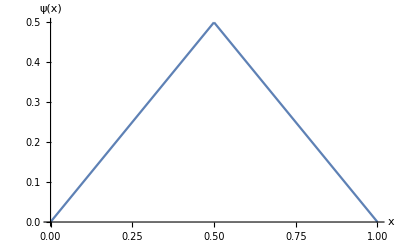

```mathematica
Plot[psi[x,1,1],{x,0,1},AxesLabel->{Style["x",FontSize->14,FontWeight->Bold],Style["ψ(x)",FontSize->14,FontWeight->Bold]}]
```

```mathematica
ψ(x)=Piecewise[{{(A x)/a, 0<x<a/2}, {A (1-x/a), a/2<x<a}}]
```

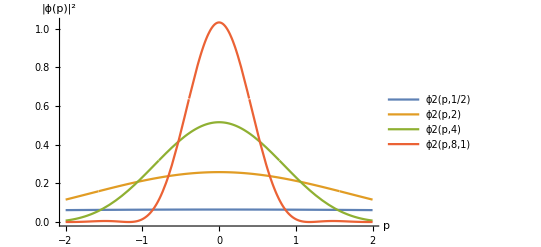

```mathematica
ℏ=1;
ϕ2[p_,a_]:=(4 π)/(ℏ a^3)Cos[(p a)/(2ℏ)]^2/(((π/a)^2-(p/ℏ)^2)^2)
ψ2[x_,a_]:=2/a Sin[(π x)/a]^2
Plot[{ϕ2[p,1/2],ϕ2[p,2],ϕ2[p,4],ϕ2[p,8,1]},{p,-2,2},PlotLegends->"Expressions",PlotRange->All,AxesLabel->{Style["p",FontSize->14,FontWeight->Bold],Style["|ϕ(p)|^2",FontSize->14,FontWeight->Bold]}]
```

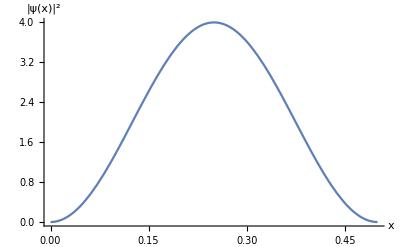

```mathematica
Plot[{ψ2[x,1/2]},{x,0,1/2},PlotLegends->"Expressions",PlotRange->All,AxesLabel->{Style["x",FontSize->14,FontWeight->Bold],Style["|ψ(x)|^2",FontSize->14,FontWeight->Bold]}]
```

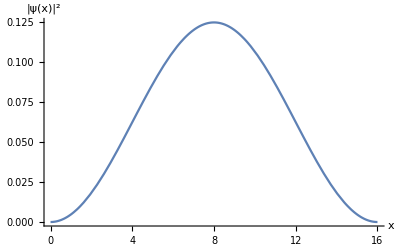

```mathematica
Plot[{ψ2[x,16]},{x,0,16},PlotLegends->"Expressions",PlotRange->All,AxesLabel->{Style["x",FontSize->14,FontWeight->Bold],Style["|ψ(x)|^2",FontSize->14,FontWeight->Bold]}]
```

```mathematica
Plot3D[ψ2[x,16]ϕ2[p,16],{x,0,16},{p,-1,1},AxesLabel->{Style["x",FontSize->14,FontWeight->Bold],Style["p",FontSize->14,FontWeight->Bold],Style["|ψ(x)|^2×|ϕ(p)|^2",FontSize->14,FontWeight->Bold]},PlotRange->All]
```

-Graphics3D-